ParametricFunction[<>]

{601.432,Null}

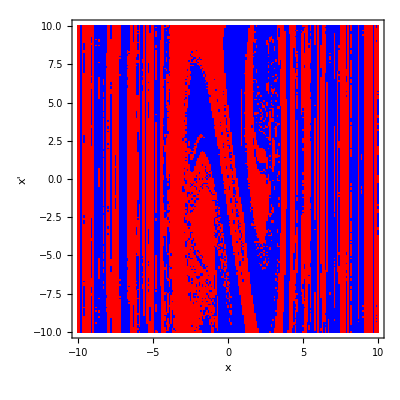

```mathematica
duffing=0.0517*x''[t]+0.01 *x'[t]-2.3 *x[t]+.3838*x[t]^3==2.9*Sin[1.884*t];
parametricsol=With[{method="DetectionMethod"->"Sign"},ParametricNDSolveValue[{duffing,x[0]==x0,x'[0]==v0,a[0]==0,WhenEvent[x[t]==#,a[t]->a[t]+#,method]&/@{-1,1},WhenEvent[a[t]==#,Sow@Sign@a[t];"StopIntegration",method]&/@{3,-3}},x,{t,0,200},{x0,v0},DiscreteVariables->a]]

value[{x_: 0}]:=x
data=With[{stepsize=1/10},ParallelTable[parametricsol[i,j]//Reap//Last//Flatten//value,{i,-10,10,stepsize},{j,-10,10,stepsize}]];//AbsoluteTiming
(*{545.779733,Null} dual core*)

ContourPlot[False,{x,-10,10},{xp,-10,10},FrameLabel->(Style[TraditionalForm@#,15]&/@{x,x'})]~Show~ArrayPlot[dataᵀ,ColorRules->{1->Red,-1->Blue,0->Yellow},DataRange->{{-10,10},{-10,10}},DataReversed->True]
```

```mathematica
.
```

ParametricFunction[<>]

{588.482,Null}

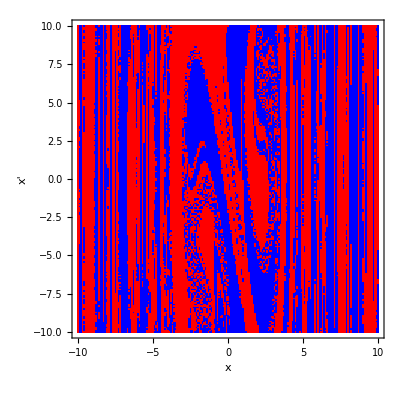

```mathematica
duffing=0.0517*x''[t]+0.01 *x'[t]-2.3 *x[t]+.3838*x[t]^3==2.75*Sin[1.884*t];
parametricsol=With[{method="DetectionMethod"->"Sign"},ParametricNDSolveValue[{duffing,x[0]==x0,x'[0]==v0,a[0]==0,WhenEvent[x[t]==#,a[t]->a[t]+#,method]&/@{-1,1},WhenEvent[a[t]==#,Sow@Sign@a[t];"StopIntegration",method]&/@{3,-3}},x,{t,0,200},{x0,v0},DiscreteVariables->a]]

value[{x_: 0}]:=x
data=With[{stepsize=1/10},ParallelTable[parametricsol[i,j]//Reap//Last//Flatten//value,{i,-10,10,stepsize},{j,-10,10,stepsize}]];//AbsoluteTiming
(*{545.779733,Null} dual core*)

ContourPlot[False,{x,-10,10},{xp,-10,10},FrameLabel->(Style[TraditionalForm@#,15]&/@{x,x'})]~Show~ArrayPlot[dataᵀ,ColorRules->{1->Red,-1->Blue,0->Yellow},DataRange->{{-10,10},{-10,10}},DataReversed->True]
```

ParametricFunction[<>]

{3089.7,Null}

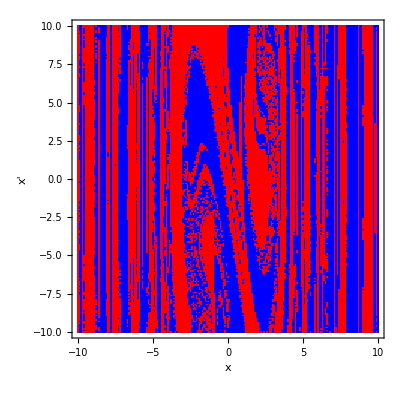

```mathematica
duffing=0.0517*x''[t]+0.01 *x'[t]-2.3 *x[t]+.3838*x[t]^3==2.7*Sin[1.884*t];
parametricsol=With[{method="DetectionMethod"->"Sign"},ParametricNDSolveValue[{duffing,x[0]==x0,x'[0]==v0,a[0]==0,WhenEvent[x[t]==#,a[t]->a[t]+#,method]&/@{-1,1},WhenEvent[a[t]==#,Sow@Sign@a[t];"StopIntegration",method]&/@{3,-3}},x,{t,0,200},{x0,v0},DiscreteVariables->a]]

value[{x_: 0}]:=x
data=With[{stepsize=1/10},ParallelTable[parametricsol[i,j]//Reap//Last//Flatten//value,{i,-10,10,stepsize},{j,-10,10,stepsize}]];//AbsoluteTiming
(*{545.779733,Null} dual core*)

ContourPlot[False,{x,-10,10},{xp,-10,10},FrameLabel->(Style[TraditionalForm@#,15]&/@{x,x'})]~Show~ArrayPlot[dataᵀ,ColorRules->{1->Red,-1->Blue,0->Yellow},DataRange->{{-10,10},{-10,10}},DataReversed->True]
```